```mathematica
n=6;
α=5;
β=1.5;
γ=1;
ω=0;
λ=-2.7;
f[value_]=FullSimplify[(λ+α value*Conjugate[value]+ β Re[value^n]+ω I)value+ γ Conjugate[value]^(n-1)];
z0=.5+.5I;

AbsoluteTiming[
dat=Quiet@ReIm@NestList[f,z0,1000000];
res=150;
epsilon=1*^-10;

indices=1+Floor[(1-epsilon) res Rescale[dat]];
System`SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->Total}];
matrix=SparseArray[indices->1.,{res,res}];
System`SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->First}];

Image[1-Rescale[matrix^(1/4)],ImageSize->Large]
]
```

{4.95557,-Graphics-}

```mathematica
AbsoluteTiming[

data = NestList[f,z0,1000000];
With[{bc=BinCounts[ReIm@data,Sequence@@({#1,#2,(#2-#1)/256}&@@@CoordinateBounds@ReIm@data)]},bc/.Map[Evaluate[#->ColorData["SunsetColors"]@N@CDF[HistogramDistribution@Flatten@bc,#]&],Union@Flatten@bc]]//Image
]
```

{44.2682,-Graphics-}

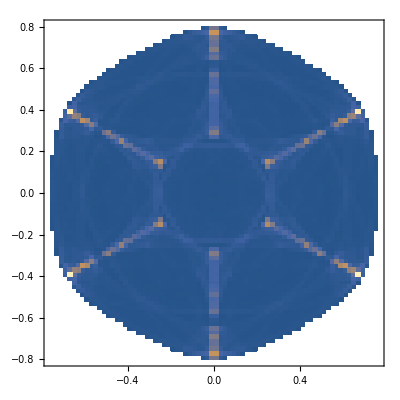
{5.97955,-Graphics-}

```mathematica
AbsoluteTiming[data=ReIm@NestList[f,z0,1000000];

DensityHistogram[data,100,"PDF"]]
```

```mathematica
AbsoluteTiming[Image[Graphics[{Black,Opacity[.05],PointSize[Tiny],Point@ReIm@NestList[f,z0,1000000]}],ImageResolution->50,ImageSize->Large]]
```

{5.86865,-Graphics-}

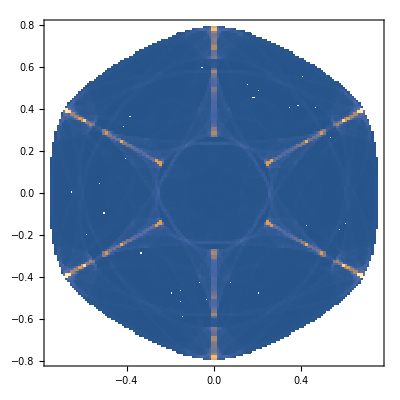
{24.4424,-Graphics-}

```mathematica
n=6;
α=5;
β=1.5;
γ=1;
ω=0;
λ=-2.7;
f[value_]=FullSimplify[(λ+α value*Conjugate[value]+ β Re[value^n]+ω I)value+ γ Conjugate[value]^(n-1)];
z0=.5+.5I;
AbsoluteTiming[
DensityHistogram[ReIm@NestList[f,z0,1000000],200,PDF]
]
```

```mathematica
list =
```